```mathematica
Clear["Global`*"]
```

```mathematica
IntervalRect[{min_,max_}]:=Rectangle[{min,0},{max,1}]
IntervalRect[{min_,max_},kappamax_]:=Rectangle[{min,0},{Min[max,kappamax],1}]
spectrum[list_,max_]:=Graphics[{Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
spectrumIntervals[list_,max_,roots_]:=Graphics[{Lighter[Blue,0.85],IntervalRect[#,max]&/@roots,Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
InverseParticipationRatio[v_]:=Norm[Normalize[v],4]^4
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
g[i_,k_]:=x[i,k][t]^phi[[i]];
m[i_,k_]:=x[i,k][t]^mu[[i]];
f[i_,k_]:=t[i,k]x[i,k][t]^psi[[i]](1+Kf[i])/(t[i,k]+Kf[i]);
Kf[i_]:=gamma[[i]]/(1-gamma[[i]]);
t[i_,k_]:=(Sum[A[[i,j]]x[j,k][t],{j,S}])
lo[i_,j_,k_]:=x[i,k][t]^psi[[i]]x[j,k][t](1+Kf[i])/(Kf[i]+t[i,k])
e[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Import and set parameters

```mathematica
InitParameterZeros[S_]:=Module[{},
alpha=Table[0,S];

sigma=Table[0,S];
sigmatilde=Table[0,S];
delta=Table[0,S];
deltatilde=Table[0,S];
beta=Table[0,S,S];

psi=Table[0,S];
phi=Table[0,S];
mu=Table[0,S];
gamma=Table[0,S];

M=Table[0,S];
d=Table[0,S];
];

(* Spatial web *)
LoadSpatialWeb6Patch[]:=Module[{},
Nvertices=6;
L={{3,-1,-1,0,0,-1},{-1,3,-1,0,-1,0},{-1,-1,2,0,0,0},{0,0,0,1,0,-1},{0,-1,0,0,1,0},{-1,0,0,-1,0,2}};
];
```

### 4 Species System

```mathematica
Load4SpeciesParameters[]:=Module[{},
S=4;
index=37;

(*load parameters from file*)
ParLocDyn5=Partition[Import["/home/brechtel/Dokumente/nphys/Data/PAR_4_1_0_0.33.txt","Table"],S+2][[All,2;;-2]];
MA1LocDyn5=Take[Partition[Import["/home/brechtel/Dokumente/nphys/Data/MA1_4_1_0_0.33.txt","Table"],S+1],{1,-1,5+2}][[All,2;;-1]];

(*set parameters*)
InitParameterZeros[S];
niche=ParLocDyn5[[index]][[1;;S,2]];
lima=Transpose[MA1LocDyn5[[index]]];

For[i=1,i≤S,++i,
(*body mass*)
M[[i]]=10^(4niche[[i]]);

(*migration rate*)
d[[i]]=2. 10^-2 M[[i]]^-1;

(*biomass flow*)
alpha[[i]]=ParLocDyn5[[index]][[i,-1]];

(*exponent parameters*)
psi[[i]]=ParLocDyn5[[index]][[i,14]];
phi[[i]]=ParLocDyn5[[index]][[i,13]];
mu[[i]]=ParLocDyn5[[index]][[i,18]];
gamma[[i]]=ParLocDyn5[[index]][[i,16]];

(*scale parameters*)
sigma[[i]]=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

(0. | 0.454909 | 0. | 0.545091
0. | 0. | 0. | 1.
0. | 1. | 0. | 0.
0. | 0. | 0. | 0.)

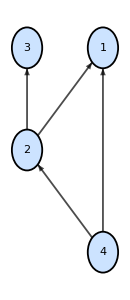

```mathematica
Load4SpeciesParameters[]
MatrixForm[A]
plt5s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
```

### 5 Species System (oscillation)

```mathematica
Load5SpeciesParameters[]:=Module[{},
S=5;
index=1;

(*load parameters from file*)
ParLocDyn5=Partition[Import["/home/brechtel/Dokumente/nphys/Data/Oszillation/PAR.txt","Table"],S+2][[All,2;;-2]];

MA1LocDyn5=Take[Partition[Import["/home/brechtel/Dokumente/nphys/Data/Oszillation/MA.txt","Table"],S+1],{1,-1,5+2}][[All,2;;-1]];

(*set parameters*)
InitParameterZeros[S];
niche=ParLocDyn5[[index]][[1;;S,2]];
lima=Transpose[MA1LocDyn5[[index]]];

For[i=1,i≤S,++i,
(*body mass*)
M[[i]]=10^(8niche[[i]]);

(*migration rate*)
d[[i]]=10^1  M[[i]]^-1;

(*biomass flow*)
alpha[[i]]=ParLocDyn5[[index]][[i,-1]];

(*exponent parameters*)
psi[[i]]=ParLocDyn5[[index]][[i,14]];
phi[[i]]=ParLocDyn5[[index]][[i,13]];
mu[[i]]=ParLocDyn5[[index]][[i,18]];
gamma[[i]]=ParLocDyn5[[index]][[i,16]];

(*scale parameters*)
sigma[[i]]=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

(0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0.)

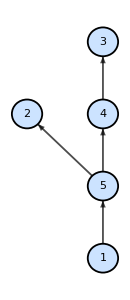

```mathematica
Load5SpeciesParameters[]
MatrixForm[A]
plt5s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
```

```mathematica
(*Export["5SpeciesWebOscillation.svg",plt5s];*)
```

### 4 Species Parameters

```mathematica
Load4SpeciesParameters2[]:=Module[{i,j},
S=4;

(*set parameters*)
InitParameterZeros[S];

lima={{0.,0.5,0.,0.5},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.}};

(*biomass flow*)
alpha={0.10,0.45,0.12,0.75};

(*exponent parameters*)
psi={1.,1.,1.,0.};
phi={0.,0.,0.,1.};
mu={1.,1.,1.,1.};
gamma={0.95,0.95,0.95,0.95};

(*migration rate*)
d={0.01,0.01,0.01,0.01};

For[i=1,i≤S,++i,
(*scale parameters*)
sigma[[i]]=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

```mathematica
Load4SpeciesParameters2[]
MatrixForm[A]
plt4s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
beta//MatrixForm
```

(0. | 0.5 | 0. | 0.5
0. | 0. | 0. | 1.
0. | 1. | 0. | 0.
0. | 0. | 0. | 0.)

-Graphics-

(0 | 0.333333 | 0 | 0.333333
0 | 0. | 0 | 0.666667
0 | 0.666667 | 0 | 0.
0 | 0. | 0 | 0.)

```mathematica
Load4SpeciesParameters3[]:=Module[{i,j},
S=4;

(*set parameters*)
InitParameterZeros[S];

lima={{0.,0.5,0.,0.5},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.}};

(*biomass flow*)
alpha={0.10,0.45,0.12,0.75};

(*exponent parameters*)
psi={1.,1.,1.,0.};
phi={0.,0.,0.,0.93};
mu={1.,1.,1.,1.};
gamma={0.95,0.95,0.95,0.95};

(*migration rate*)
d={0.01,0.01,0.01,0.01};

For[i=1,i≤S,++i,
(*scale parameters*)
sigma[[i]]=Sum[lima[[n,i]],{n,S}]/(Sum[lima[[n,i]],{n,S}]+1);
sigmatilde[[i]]=1-sigma[[i]];

If[Sum[lima[[i,j]],{j,S}]>0,delta[[i]]=1,delta[[i]]=0];
deltatilde[[i]]=1-delta[[i]];

For[j=1,j≤S,++j,beta[[j,i]]=If[sigma[[i]]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0]];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=3;
];
```

```mathematica
Load4SpeciesParameters3[]
MatrixForm[A]
plt4s=GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->{130,300}
]
beta//MatrixForm
```

(0. | 0.5 | 0. | 0.5
0. | 0. | 0. | 1.
0. | 1. | 0. | 0.
0. | 0. | 0. | 0.)

-Graphics-

(0 | 0.333333 | 0 | 0.333333
0 | 0. | 0 | 0.666667
0 | 0.666667 | 0 | 0.
0 | 0. | 0 | 0.)

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[i_,k_]:=alpha[[i]](deltatilde[[i]]g[i,k]
+delta[[i]]If[Sum[lima[[i,j]],{j,S}]>0,f[i,k],0]
-sigmatilde[[i]]m[i,k]
-sigma[[i]]Sum[beta[[j,i]]If[beta[[j,i]]>0,lo[j,i,k],0],{j,S}])
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==0.1 (0.-1. (x[1,1][t])^1.+(20. (x[1,1][t])^1. (0.+0.5 x[2,1][t]+0.5 x[4,1][t]))/(19.+0.5 x[2,1][t]+0.5 x[4,1][t])),x[2,1]'[t]==0.45 (0.-0.4 (x[2,1][t])^1.-0.6 (0.+(13.3333 x[2,1][t] (x[3,1][t])^1.)/(19.+1. x[2,1][t])+(6.66667 (x[1,1][t])^1. x[2,1][t])/(19.+0.5 x[2,1][t]+0.5 x[4,1][t]))+(20. (x[2,1][t])^1. (0.+1. x[4,1][t]))/(19.+1. x[4,1][t])),x[3,1]'[t]==0.12 (0.-1. (x[3,1][t])^1.+(20. (0.+1. x[2,1][t]) (x[3,1][t])^1.)/(19.+1. x[2,1][t])),x[4,1]'[t]==0.75 ((x[4,1][t])^0.93-0.4 (x[4,1][t])^1.-0.6 (0.+(6.66667 (x[1,1][t])^1. x[4,1][t])/(19.+0.5 x[2,1][t]+0.5 x[4,1][t])+(13.3333 (x[2,1][t])^1. x[4,1][t])/(19.+1. x[4,1][t])))}

## Jacobian

```mathematica
CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.Table[x[i,1][t]->1,{i,S}]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateMSF[]:=Module[{points,dkappa=0.1},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];
points=Table[{kappa,Max[Re[Eigenvalues[J0-kappa JM]]]},{kappa,-10,kappamax,dkappa}];
MSF=Interpolation[points,InterpolationOrder->1];
Return[MSF]
];

CalculateReCoMSF[]:=Module[{points,dkappa=0.01,kappa},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];

RePoints={};
CoPoints={};

For[kappa=-1,kappa≤kappamax,kappa+=dkappa,
EV=First[MaximalBy[ReIm[Eigenvalues[J0-kappa JM]],First]];
If[Abs[EV[[2]]]==0,
AppendTo[RePoints,{kappa,EV[[1]]}];
,
AppendTo[CoPoints,{kappa,EV[[1]]}];
];
];
];

PlotCoReMSF[RePoints_,CoPoints_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->{{0,kappamax},Automatic}
]
];
]

PlotCoReMSF[RePoints_,CoPoints_,plotRange_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->plotRange
]
];
]

(*Find unstable interval*)
FindUnstableInterval[MSF_]:=Module[{kappa0,kappa,step=0.001,roots},
intervals={};
roots={};
If[!ValueQ[kappamax],kappamax=15];

For[kappa=0,kappa+step≤kappamax,kappa+=step,
If[MSF[kappa]MSF[kappa+step]<0,AppendTo[roots,kappa+step/2]];
];

If[Length[roots]==0,
Print["Failed to find unstable interval."];
Abort[];
];

For[i=1,i≤Length[roots],i+=2,
If[i+1≤Length[roots],
AppendTo[intervals,{roots[[i]],roots[[i+1]]}],
Print["Failed to find maximum of the last unstable interval. Set maximum to kappamax."];
AppendTo[intervals,{roots[[i]],kappamax}];
];
];

interval=First[intervals];
];
```

Failed to find unstable interval.

$Aborted

{}

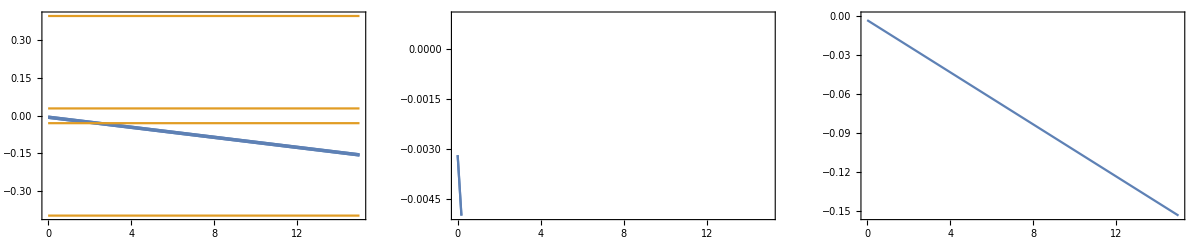

```mathematica
CalculateJacobian[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];
intervals

GraphicsRow[{
Plot[{Sort[Re[Eigenvalues[J0-kappa JM]]],Sort[Im[Eigenvalues[J0-kappa JM]]]},{kappa,0,kappamax},PlotRange->Full,Frame->True,ImageSize->Medium],
Plot[{Sort[Re[Eigenvalues[J0-kappa JM]]],Sort[Im[Eigenvalues[J0-kappa JM]]]},{kappa,0,kappamax},PlotRange->{-0.005,0.001},Frame->True,ImageSize->Medium],
Plot[MSF[kappa],{kappa,0,kappamax},Frame->True,ImageSize->Medium]
}]

If[ValueQ[kappaList],spectrumIntervals[kappaList,kappamax,intervals]]
```

```mathematica
kappa=0;
ReIm[Eigenvalues[J0-kappa JM]]
MaximalBy[ReIm[Eigenvalues[J0-kappa JM]],First]
```

{{-0.00318321,0.397259},{-0.00318321,-0.397259},{-0.00806679,0.029348},{-0.00806679,-0.029348}}

{{-0.00318321,0.397259},{-0.00318321,-0.397259}}

0.5

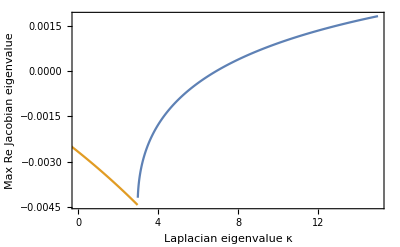

```mathematica
Load4SpeciesParameters[];
phi[[4]]=0.5
CalculateReCoMSF[];
MSFPlot1=PlotCoReMSF[RePoints,CoPoints]
```

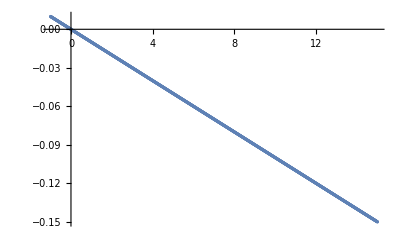

```mathematica
Load4SpeciesParameters2[];
phi[[4]]=0.94;
CalculateReCoMSF[];
MSFPlot1=ListPlot[CoPoints]
```

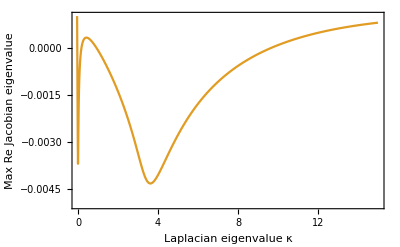

```mathematica
Load5SpeciesParameters[];
CalculateReCoMSF[];
MSFPLot2=PlotCoReMSF[RePoints,CoPoints,{{0,kappamax},{-0.005,0.001}}]
```

```mathematica
(*Export["MSF4S.pdf",MSFPlot1]
Export["MSF5S.pdf",MSFPLot2]*)
```

## Spatial Web

```mathematica
FindSpacialWeb[nvertices_,r_,n_]:=Module[{maxtries,tries},
Nvertices=nvertices;
R=r;

maxtries=1000;
tries=0;
While[tries<maxtries,
++tries;
graph=RandomGraph[SpatialGraphDistribution[Nvertices,R/Sqrt[Nvertices]]];
If[!ConnectedGraphQ[graph],Continue[]];
L=KirchhoffMatrix[graph];
kappaList=N[Eigenvalues[L]];
If[ValueQ[intervals],
If[Count[kappaList,x_/;Apply[Or,Table[intervals[[i,1]]<x<intervals[[i,2]],{i,Length[intervals]}]]]==n,
If[n>0,unstable=Position[kappaList,x_/;Apply[Or,Table[intervals[[i,1]]<x<intervals[[i,2]],{i,Length[intervals]}]]][[1,1]];
];
Break[]],
Break[]]
];
If[tries==maxtries,Print["No matching spatial web found after "<>ToString[maxtries]" tries."],Print["Matching spatial web found after "<>ToString[tries]" tries."]];
vlist=N[Eigenvectors[L]];
If[!ValueQ[unstable],unstable=1];
If[!ValueQ[kappamax],kappamax=Ceiling[Max[kappaList],5]];
];

FindUnstableSpatialWeb[Nvertices_,R_]:=FindSpacialWeb[Nvertices,R,1];
FindStableSpatialWeb[Nvertices_,R_]:=FindSpacialWeb[Nvertices,R,0];

ShowSpatialWeb[]:=Module[{},
Print[graph];
If[ValueQ[intervals],
Print[spectrumIntervals[Eigenvalues[L],kappamax,intervals]],
Print[spectrum[Eigenvalues[L],kappamax]]
]
];
```

Failed to find maximum of the last unstable interval. Set maximum to kappamax.

Matching spatial web found after 5  tries.

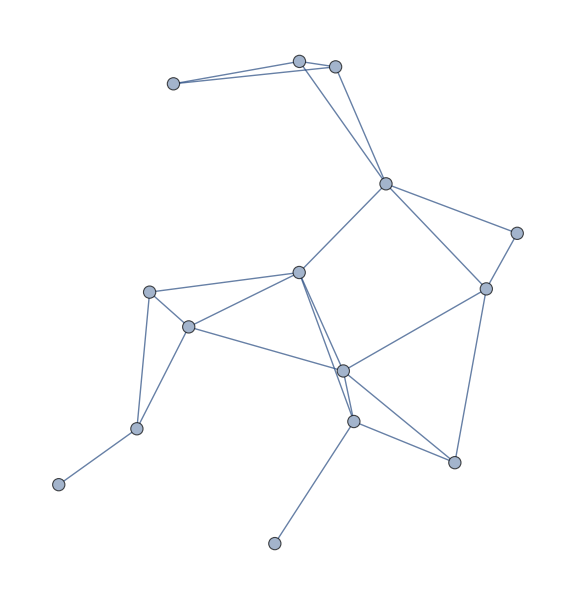

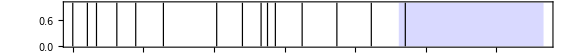

```mathematica
Load4SpeciesParameters[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];

Clear[kappamax];
Np=15;
FindSpacialWeb[Np,1.3,1];
ShowSpatialWeb[];
```

Failed to find maximum of the last unstable interval. Set maximum to kappamax.

Matching spatial web found after 7  tries.

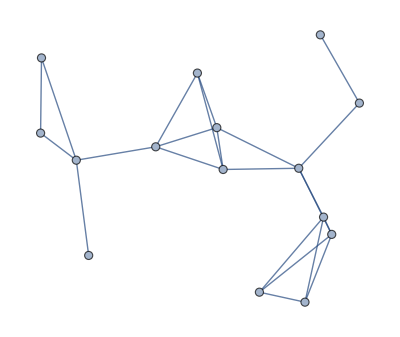

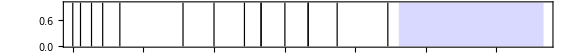

```mathematica
Load4SpeciesParameters[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];

Clear[kappamax];
FindSpacialWeb[15,1.3,0];
ShowSpatialWeb[];
```

```mathematica
(* Stable for 4 species system *)
LoadSpatialWeb[]:=Module[{},
Nvertices=15;
L={{4,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,-1},{0,3,0,-1,-1,0,0,0,0,-1,0,0,0,0,0},{0,0,2,0,0,0,0,-1,0,0,-1,0,0,0,0},{0,-1,0,3,-1,0,0,0,0,0,-1,0,0,0,0},{0,-1,0,-1,3,-1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,4,0,0,0,0,0,0,-1,0,-1},{-1,0,0,0,0,0,3,0,0,0,0,-1,0,0,-1},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,3,0,-1,0,-1,-1,0},{0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,-1,-1,0,0,0,0,-1,0,5,0,-1,-1,0},{-1,0,0,0,0,0,-1,0,0,0,0,3,0,0,-1},{0,0,0,0,0,-1,0,0,-1,0,-1,0,4,-1,0},{0,0,0,0,0,0,0,0,-1,0,-1,0,-1,3,0},{-1,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,4}};
graph=KirchhoffGraph[L];
];
```

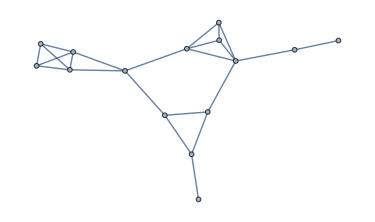

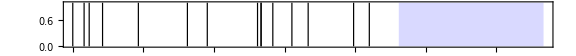

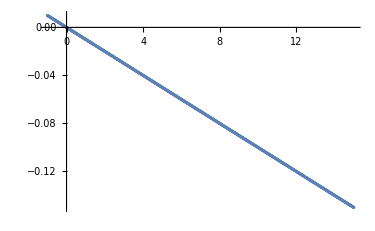

```mathematica
LoadSpatialWeb[];
ShowSpatialWeb[];
MSFPlot1
```

## Eigenvalues

(0. | 0.0475 | 0 | 0.0475
-0.09 | 0.01125 | -0.18 | 0.42975
0 | 0.114 | 0. | 0
-0.15 | -0.29625 | 0 | 0.75 (-0.975+ϕ))

(0.01 | 0. | 0. | 0.
0. | 0.01 | 0. | 0.
0. | 0. | 0.01 | 0.
0. | 0. | 0. | 0.01)

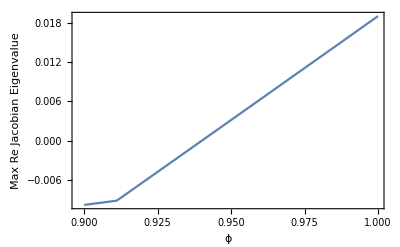

```mathematica
Load4SpeciesParameters2[]
LoadSpatialWeb[];
phi[[4]]=ϕ;
CalculateJacobian[];
MatrixForm[J0]
MatrixForm[JM]
list=Table[{ϕ,Max[Re[Eigenvalues[J0]]]},{ϕ,0.9,1.,0.001}];
plot=ListLinePlot[list,Frame->True,FrameLabel->{ϕ,"Max Re Jacobian Eigenvalue"}]
(*TableForm[list]*)
(*Export["BiggerSystemLocalJacobianEigenvalues.pdf",plot]
Export["BiggerSystemLocalJacobianEigenvalues.CSV",list]*)
```

```mathematica
Load4SpeciesParameters3[]
LoadSpatialWeb[];
phi[[4]]=ϕ;
CalculateJacobian[];
KappaList=N[Eigenvalues[L]];
list=Table[{ϕ,Max[Re[Table[Eigenvalues[J0-kappa JM],{kappa,KappaList}]]]},{ϕ,0.9,1.,0.001}];
plot=ListLinePlot[list,Frame->True,FrameLabel->{ϕ,"Max Re Jacobian Eigenvalue"}]

(*Export["4S6P-mu=2-JacobianEigenvalues.pdf",plot]
Export["4S6P-mu=2-JacobianEigenvalues.CSV",list]*)
```

-Graphics-

```mathematica
Table[{ϕ,Table[Eigenvalues[J0-kappa JM],{kappa,KappaList}]},{ϕ,0.94,0.941,0.001}]//TableForm
```

0.94 | -0.0630018+0.397508 ⅈ | -0.0630018-0.397508 ⅈ | -0.0704765+0.0294824 ⅈ | -0.0704765-0.0294824 ⅈ
-0.0596666+0.397508 ⅈ | -0.0596666-0.397508 ⅈ | -0.0671413+0.0294824 ⅈ | -0.0671413-0.0294824 ⅈ
-0.0500127+0.397508 ⅈ | -0.0500127-0.397508 ⅈ | -0.0574873+0.0294824 ⅈ | -0.0574873-0.0294824 ⅈ
-0.0465599+0.397508 ⅈ | -0.0465599-0.397508 ⅈ | -0.0540346+0.0294824 ⅈ | -0.0540346-0.0294824 ⅈ
-0.042506+0.397508 ⅈ | -0.042506-0.397508 ⅈ | -0.0499807+0.0294824 ⅈ | -0.0499807-0.0294824 ⅈ
-0.0400127+0.397508 ⅈ | -0.0400127-0.397508 ⅈ | -0.0474873+0.0294824 ⅈ | -0.0474873-0.0294824 ⅈ
-0.0400127+0.397508 ⅈ | -0.0400127-0.397508 ⅈ | -0.0474873+0.0294824 ⅈ | -0.0474873-0.0294824 ⅈ
-0.0392578+0.397508 ⅈ | -0.0392578-0.397508 ⅈ | -0.0467325+0.0294824 ⅈ | -0.0467325-0.0294824 ⅈ
-0.0285844+0.397508 ⅈ | -0.0285844-0.397508 ⅈ | -0.0360591+0.0294824 ⅈ | -0.0360591-0.0294824 ⅈ
-0.0243609+0.397508 ⅈ | -0.0243609-0.397508 ⅈ | -0.0318356+0.0294824 ⅈ | -0.0318356-0.0294824 ⅈ
-0.0139453+0.397508 ⅈ | -0.0139453-0.397508 ⅈ | -0.02142+0.0294824 ⅈ | -0.02142-0.0294824 ⅈ
-0.00633946+0.397508 ⅈ | -0.00633946-0.397508 ⅈ | -0.0138142+0.0294824 ⅈ | -0.0138142-0.0294824 ⅈ
-0.00349907+0.397508 ⅈ | -0.00349907-0.397508 ⅈ | -0.0109738+0.0294824 ⅈ | -0.0109738-0.0294824 ⅈ
-0.00241804+0.397508 ⅈ | -0.00241804-0.397508 ⅈ | -0.00989273+0.0294824 ⅈ | -0.00989273-0.0294824 ⅈ
-0.0000126508+0.397508 ⅈ | -0.0000126508-0.397508 ⅈ | -0.00748735+0.0294824 ⅈ | -0.00748735-0.0294824 ⅈ
0.941 | -0.0626846+0.39753 ⅈ | -0.0626846-0.39753 ⅈ | -0.0704187+0.0294953 ⅈ | -0.0704187-0.0294953 ⅈ
-0.0593494+0.39753 ⅈ | -0.0593494-0.39753 ⅈ | -0.0670834+0.0294953 ⅈ | -0.0670834-0.0294953 ⅈ
-0.0496955+0.39753 ⅈ | -0.0496955-0.39753 ⅈ | -0.0574295+0.0294953 ⅈ | -0.0574295-0.0294953 ⅈ
-0.0462427+0.39753 ⅈ | -0.0462427-0.39753 ⅈ | -0.0539767+0.0294953 ⅈ | -0.0539767-0.0294953 ⅈ
-0.0421888+0.39753 ⅈ | -0.0421888-0.39753 ⅈ | -0.0499229+0.0294953 ⅈ | -0.0499229-0.0294953 ⅈ
-0.0396955+0.39753 ⅈ | -0.0396955-0.39753 ⅈ | -0.0474295+0.0294953 ⅈ | -0.0474295-0.0294953 ⅈ
-0.0396955+0.39753 ⅈ | -0.0396955-0.39753 ⅈ | -0.0474295+0.0294953 ⅈ | -0.0474295-0.0294953 ⅈ
-0.0389406+0.39753 ⅈ | -0.0389406-0.39753 ⅈ | -0.0466747+0.0294953 ⅈ | -0.0466747-0.0294953 ⅈ
-0.0282672+0.39753 ⅈ | -0.0282672-0.39753 ⅈ | -0.0360013+0.0294953 ⅈ | -0.0360013-0.0294953 ⅈ
-0.0240437+0.39753 ⅈ | -0.0240437-0.39753 ⅈ | -0.0317778+0.0294953 ⅈ | -0.0317778-0.0294953 ⅈ
-0.0136281+0.39753 ⅈ | -0.0136281-0.39753 ⅈ | -0.0213622+0.0294953 ⅈ | -0.0213622-0.0294953 ⅈ
-0.00602229+0.39753 ⅈ | -0.00602229-0.39753 ⅈ | -0.0137563+0.0294953 ⅈ | -0.0137563-0.0294953 ⅈ
-0.0031819+0.39753 ⅈ | -0.0031819-0.39753 ⅈ | -0.0109159+0.0294953 ⅈ | -0.0109159-0.0294953 ⅈ
-0.00210087+0.39753 ⅈ | -0.00210087-0.39753 ⅈ | -0.0098349+0.0294953 ⅈ | -0.0098349-0.0294953 ⅈ
0.000304517+0.39753 ⅈ | 0.000304517-0.39753 ⅈ | -0.00742952+0.0294953 ⅈ | -0.00742952-0.0294953 ⅈ

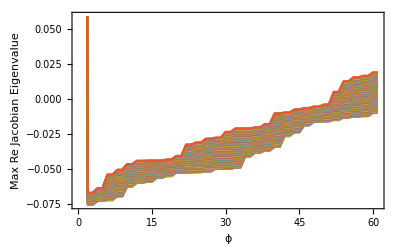

```mathematica
Load4SpeciesParameters3[]
LoadSpatialWeb[];
phi[[4]]=ϕ;
CalculateJacobian[];
KappaList=N[Eigenvalues[L]];
list=Table[Flatten[{ϕ,Sort[Flatten[Re[N[Table[Eigenvalues[J0-kappa JM],{kappa,KappaList}]]]]]}],{ϕ,0.9,1.,0.001}];
plot=ListLinePlot[list,Frame->True,FrameLabel->{ϕ,"Max Re Jacobian Eigenvalue"}]
```

```mathematica
list[[3]]
```

{0.902,-0.0750379,-0.0750379,-0.0726904,-0.0726904,-0.0717027,-0.0717027,-0.0693552,-0.0693552,-0.0620488,-0.0620488,-0.0597012,-0.0597012,-0.058596,-0.058596,-0.0562485,-0.0562485,-0.0545421,-0.0545421,-0.0521946,-0.0521946,-0.0520488,-0.0520488,-0.0520488,-0.0520488,-0.0512939,-0.0512939,-0.0497012,-0.0497012,-0.0497012,-0.0497012,-0.0489464,-0.0489464,-0.0406205,-0.0406205,-0.038273,-0.038273,-0.036397,-0.036397,-0.0340495,-0.0340495,-0.0259814,-0.0259814,-0.0236339,-0.0236339,-0.0183756,-0.0183756,-0.0160281,-0.0160281,-0.0155352,-0.0155352,-0.0144541,-0.0144541,-0.0131877,-0.0131877,-0.0121066,-0.0121066,-0.0120488,-0.0120488,-0.00970125,-0.00970125}

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Sorted Models/Bigger System/export"];
Export["BiggerSystemAllEigenvalues.CSV",list]
```

BiggerSystemAllEigenvalues.CSV

## Fixed Points

```mathematica
(*PreyList={};
PredatorList={};
min=0.1;max=0.2;
steps=10;
step=(max-min)/steps;
For[i=1,i<steps,++i,
par=min+i*step;
phi[[4]]=par;
SteadyStates=NSolve[{rhs[1,1]==0,rhs[2,1]==0,rhs[3,1]==0,rhs[4,1]==0},{x[1,1][t],x[2,1][t],x[3,1][t],x[4,1][t]}];
AppendTo[PreyList,{par,x[1,1][t]}/.SteadyStates];
AppendTo[PredatorList,{par,x[2,1][t]}/.SteadyStates];
];
PreyList=Flatten[PreyList,1];
PredatorList=Flatten[PredatorList,1];
GraphicsRow[{ListPlot[PreyList,PlotRange->All],
ListPlot[PredatorList,PlotRange->All]}]*)
```

## Homogeneous System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
x[i,k][0]==RandomReal[{1-delta,1+delta}],
{i,S},{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
(*TS[i]=Sum[c[[i,j]]XS[j],{j,S}];*)
];
];
```

## Spatial System

```mathematica
(*set starting conditions*)
setStartSpatial[]:=Module[{delta=0.01},
startSpatial=
Flatten[
Table[
x[i,k][0]==RandomReal[{1-delta,1+delta}],
{i,S},{k,Nvertices}]
];
];

(*Solve ODE*)
solveSpatial[Tmax_]:=Module[{sol},
setStartSpatial[];
sol=NDSolve[Join[{eqnsSpatial,startSpatial}],varsSpatial,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsSpatial/.sol];
];

EvaluateSpatialSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsSpatial=Flatten[Table[
x[i,k]'[t]==rhs[i,k]+e[i,k],
{i,S},{k,1Nvertices}]];

(*dependent variables*)
varsSpatial = Flatten[
Table[
x[i,k][t]
,{i,S},{k,Nvertices}]
];

(*solve deqns*)
solSpatial=solveSpatial[Tmax];
XSList=solSpatial/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
(*TS[i]=Sum[c[[i,j]]XS[j],{j,S}];*)
];
];
```

## Solver

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocal[]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocal[noise_,tmax_,maxSteps_]:=Module[{y},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1;
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaLocal[noise_]:=Module[{y},
EulerMaruyamaLocal[noise,100,100000];
];
```

### Spatial

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatial[Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.01,0.01}];
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];
```

```mathematica
EulerMaruyamaSpatial[noise_, Tmax_, maxsteps_, initialData_] := Module[{y},
   dt = Tmax/maxsteps;
   
   (*noise=0.01;*)
   Noise[] := Table[RandomVariate[NormalDistribution[0, Sqrt[dt]]], {S}, {Nvertices}];
   
   data = Table[0, {maxsteps}, {i, S}, {k, Nvertices}];
   eqns = FullSimplify[Table[rhs[i, k] + e[i, k], {i, S}, {k, Nvertices}]] /. Flatten[Table[(x[i, k][t]) -> y[i, k], {i, S}, {k, Nvertices}]];
   
   data[[1]] = initialData;
   
   For[step = 1, step < maxsteps, step++,
    For[i = 1, i <= S, ++i,
     For[k = 1, k <= Nvertices, ++k,
       y[i, k] = data[[step, i, k]];
       ];
     ];
    data[[step + 1]] = data[[step]] + eqns dt + noise Sqrt[data[[step]]] Noise[];
    data[[step + 1]] = data[[step + 1]] /. {x_?Negative -> 0};
    ];
   ];
```

```mathematica
EulerMaruyamaSpatialSaveSteps[noise_,Tmax_,maxSteps_,saveSteps_]:=Module[{y,data0,data1,step,sstep,interSteps},
dt=Tmax/maxSteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{saveSteps},{i,S},{k,Nvertices}];
data0=Table[0,{i,S},{k,Nvertices}];
data1=Table[0,{i,S},{k,Nvertices}];

eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data0[[i,k]]=1;
];
];
data[[1]]=data0;

interSteps=maxSteps/saveSteps;
For[sstep=1,sstep<saveSteps,sstep++,
For[step=1,step<interSteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data0[[i,k]];
];
];
data1=data0+eqns dt+noise Sqrt[data0]Noise[];
data1=data1/.{x_?Negative->0};
data0=data1;
];
data[[sstep+1]]=data0
];
];
```

```mathematica
EulerMaruyamaSpatialSaveSteps[noise_,Tmax_,maxSteps_,saveSteps_,initialData_]:=Module[{y,data0,data1,step,sstep,interSteps},
dt=Tmax/maxSteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{saveSteps},{i,S},{k,Nvertices}];
data0=Table[0,{i,S},{k,Nvertices}];
data1=Table[0,{i,S},{k,Nvertices}];

eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data0=initialData;
data[[1]]=data0;

interSteps=maxSteps/saveSteps;
For[sstep=1,sstep<saveSteps,sstep++,
For[step=1,step≤interSteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data0[[i,k]];
];
];
data1=data0+eqns dt+noise Sqrt[data0]Noise[];
data1=data1/.{x_?Negative->0};
data0=data1;
];
data[[sstep+1]]=data0;
];
];
```

### Local variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocalVariable[Interval_]:=Module[{y,phistep,phit,step},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocalVariable[Interval_,noise_,tmax_,maxSteps_]:=Module[{y,phistep,phit,step},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.01,0.01}];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaLocalVariable[Interval_,noise_]:=Module[{y},
EulerMaruyamaLocalVariable[Interval,noise,100,100000];
];
```

### Spatial variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariable[Interval_]:=Module[{y,phistep,phit,step},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.01,0.01}];
];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariable[Interval_,noise_,tmax_,maxSteps_]:=Module[{y,phistep,phit},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaSpatialVariable[Interval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariable[Interval,noise,100,100000];
];

EulerMaruyamaSpatialVariable[Interval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,phit,phistep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
phit=Interval[[1]]+step phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];
```

```mathematica
EulerMaruyamaSpatialVariableSaveSteps[Interval_,noise_,tmax_,maxSteps_,saveSteps_,initialData_]:=Module[{y,phit,phistep,data0,data1,interSteps,step,sstep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(Interval[[2]]-Interval[[1]])/maxsteps;
phi[[4]]=phit;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data0=Table[0,{i,S},{k,Nvertices}];
data1=Table[0,{i,S},{k,Nvertices}];
data=Table[0,{saveSteps},{i,S},{k,Nvertices}];

eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data0=initialData;
data[[1]]=data0;

interSteps=maxSteps/saveSteps;
phistep=(Interval[[2]]-Interval[[1]])/(interSteps*(saveSteps-1));
phi[[4]]=phit;

For[sstep=1,sstep<saveSteps,sstep++,
For[step=1,step≤interSteps,step++,
phit=Interval[[1]]+(step +(sstep-1) interSteps) phistep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data0[[i,k]];
];
];
data1=data0+eqns dt+noise Sqrt[data0]Noise[];
data1=data1/.{x_?Negative->0};
data0=data1;
];
data[[sstep+1]]=data0;
];
];
```

### Spatial variable gamma

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariableGamma[Interval_,noise_,tmax_,maxSteps_]:=Module[{y,gammastep,gammat},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

gammastep=(Interval[[2]]-Interval[[1]])/maxsteps;
gamma=gammat{1,1,1,0};

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
gammat=Interval[[1]]+step gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaSpatialVariableGamma[Interval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariableGamma[Interval,noise,100,100000];
];

EulerMaruyamaSpatialVariableGamma[Interval_,noise_,tmax_,maxSteps_, initialData_]:=Module[{y,gammastep,gammat},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

gammastep=(Interval[[2]]-Interval[[1]])/maxsteps;
gamma=gammat{1,1,1,0};

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];


data[[1]]=initialData;


For[step=1,step<maxsteps,step++,
gammat=Interval[[1]]+step gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaSpatialVariableGammaSaveSteps[Interval_,noise_,tmax_,maxSteps_,saveSteps_,initialData_]:=Module[{y,gammat,gammastep,data0,data1,step,sstep,interSteps},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

gamma={1,1,1,0}gammat;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{saveSteps},{i,S},{k,Nvertices}];
data0=Table[0,{i,S},{k,Nvertices}];
data1=Table[0,{i,S},{k,Nvertices}];

eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data0=initialData;
data[[1]]=data0;

interSteps=maxSteps/saveSteps;
gammastep=(Interval[[2]]-Interval[[1]])/(interSteps*(saveSteps-1));

For[sstep=1,sstep<saveSteps,sstep++,
For[step=1,step≤interSteps,step++,
gammat=Interval[[1]]+(step +(sstep-1) interSteps) gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data0[[i,k]];
];
];
data1=data0+eqns dt+noise Sqrt[data0]Noise[];
data1=data1/.{x_?Negative->0};
data0=data1;
];
data[[sstep+1]]=data0;
];
];
```

## Plots

```mathematica
GenerateSpatialGraphPlot[]:=Module[{thickness=0.01},
GraphPlot[graph,
VertexRenderingFunction->Function[{p,l},{White,EdgeForm[{Thickness[thickness],RGBColor[222/255,135/255,135/255]}],Disk[p,0.25],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{RGBColor[222/255,135/255,135/255],Thickness[thickness],Line[p]}],
ImageSize->300
]
];
```

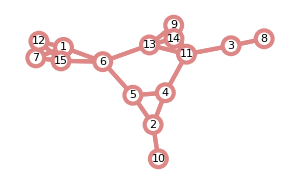

```mathematica
LoadSpatialWeb[];
graph=KirchhoffGraph[L];
plt1=GenerateSpatialGraphPlot[]
```

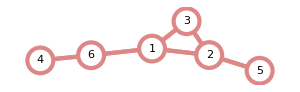

```mathematica
LoadSpatialWeb6Patch[]
graph=KirchhoffGraph[L];
plt2=GenerateSpatialGraphPlot[]
```

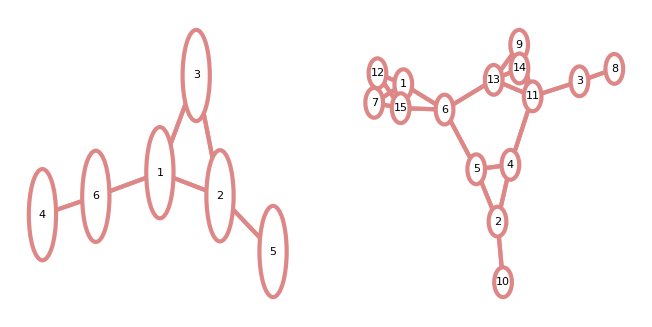

```mathematica
gr=GraphicsRow[{plt2,plt1}]
```

```mathematica
Export["SpatialWebs.pdf",gr]
```

SpatialWebs.pdf

```mathematica
Directory[]
```

/home/brechtel